```mathematica
CollectMPGEdges[g_]:=Select[EdgeList[g],MaximalPlanarQ[EdgeContract[g,#]]&]
```

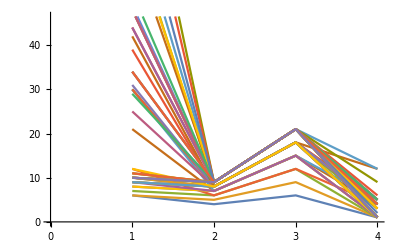

```mathematica
Table[With[{g=ReadGrof[k]},{Total[Map[ChromaticPolynomial[EdgeContract[g,#],4]/24&,CollectMPGEdges[g]]],VertexCount[g],EdgeCount[g],ChromaticPolynomial[g,4]/24}],{k,50}]//ListLinePlot
```

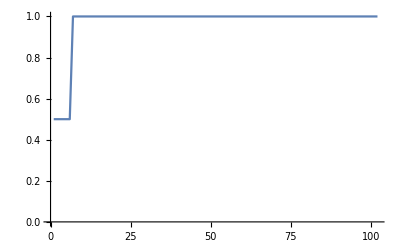

```mathematica
Monitor[ListLinePlot[Sort[Flatten[Table[With[{g=MinimalGraph[k]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,12}]]],PlotRange->All],k]
```

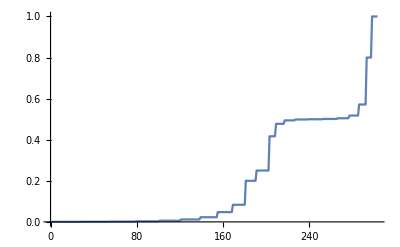

```mathematica
Monitor[ListLinePlot[Sort[Flatten[Table[With[{g=JacobsThalGraph[k]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,12}]]],PlotRange->All],k]
```

```mathematica
Monitor[Sort[Flatten[Table[With[{g=JacobsThalGraph[k]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,12}]]],k]
```

{1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/2732,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/1365,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/684,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/341,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/172,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/85,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/44,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/21,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,5/12,5/12,5/12,5/12,5/12,5/12,21/44,21/44,21/44,21/44,21/44,21/44,21/44,21/44,85/172,85/172,85/172,85/172,85/172,85/172,85/172,85/172,85/172,85/172,341/684,341/684,341/684,341/684,341/684,341/684,341/684,341/684,341/684,341/684,341/684,341/684,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,1365/2732,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,228/455,172/341,172/341,172/341,172/341,172/341,172/341,172/341,172/341,172/341,172/341,172/341,44/85,44/85,44/85,44/85,44/85,44/85,44/85,44/85,44/85,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/5,4/5,4/5,4/5,4/5,1,1,1,1,1,1}

```mathematica
Monitor[Sort[Flatten[Table[With[{g=Graph[plantri[[k]]]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,12}]]],k]
```

{1/3,1/3,4/11,4/11,4/11,3/8,3/8,3/8,3/8,3/8,3/8,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,3/7,7/16,7/16,7/16,7/16,7/16,7/16,7/16,7/16,7/16,7/16,7/16,7/16,13/27,13/27,13/27,13/27,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,8/15,8/15,8/15,8/15,8/15,8/15,9/16,9/16,9/16,9/16,9/16,9/16,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,4/7,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,5/8,5/8,5/8,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,9/14,29/44,29/44,29/44,29/44,29/44,29/44,29/44,29/44,29/44,29/44,29/44,29/44,2/3,2/3,2/3,2/3,15/22,15/22,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,19/27,19/27,19/27,19/27,11/15,11/15,11/15,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,3/4,17/22,17/22,17/22,17/22,17/22,17/22,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,13/16,13/16,13/16,13/16,13/16,13/16,13/16,13/16,27/32,27/32,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,17/20,23/27,23/27,23/27,23/27,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,13/15,7/8,7/8,7/8,7/8,8/9,8/9,8/9,8/9,8/9,8/9,8/9,8/9,14/15,14/15,14/15,14/15,14/15,14/15,15/16,15/16,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,19/20,1,1,1,1,1,1,1,1,1,1,1,1,33/32,33/32,23/22,23/22,17/16,17/16,17/16,17/16,17/16,17/16,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,16/15,29/27,29/27,35/32,11/10,11/10,11/10,11/10,11/10,11/10,11/10,11/10,11/10,11/10,9/8,9/8,9/8,9/8,17/15,17/15,17/15,17/15,17/15,17/15,7/6,7/6,7/6,7/6,7/6,7/6,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,13/11,32/27,32/27,32/27,32/27,32/27,32/27,19/16,19/16,27/22,27/22,27/22,27/22,5/4,5/4,5/4,5/4,14/11,14/11,14/11,14/11,14/11,14/11,14/11,14/11,21/16,21/16,21/16,15/11,15/11,11/8,11/8,11/8,11/8,11/8,11/8,11/8,11/8,31/22,31/22,31/22,31/22,3/2,3/2,3/2,3/2,49/32,49/32,17/11,17/11,17/11,17/11,17/11,17/11,17/11,17/11,17/11,17/11,25/16,25/16,35/22,35/22,35/22,35/22,27/16,27/16,27/16,27/16,26/15,26/15,26/15,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,7/4,15/8,15/8,15/8,15/8,15/8,15/8,2,2,2,45/22,45/22,45/22,17/8,17/8,17/8,17/8,9/4,28/11}

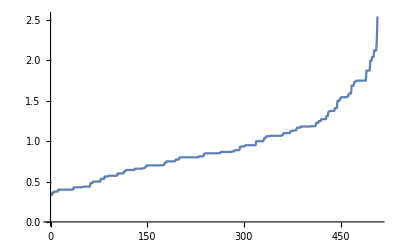

```mathematica
Monitor[ListLinePlot[Sort[Flatten[Table[With[{g=Graph[plantri[[k]]]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,12}]]],PlotRange->All],k]
```

```mathematica
Monitor[ListLinePlot[Sort[Flatten[Table[With[{g=ReadGrof[k]},With[{v=(ChromaticPolynomial[g,4])},Sort[Map[ChromaticPolynomial[EdgeContract[g,#],4]/v&,CollectMPGEdges[g]]]]],{k,500}]]],PlotRange->All],k]
```

$Aborted

```mathematica
Monitor[Table[With[{g=MinimalGraph[k]},{VertexCount[g],Length[CollectMPGEdges[g]]}],{k,4,20}],k]
```

{{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22}}

```mathematica
Table[With[{g=MinimalGraph[k]},ChromaticPolynomial[Graph[CollectMPGEdges[g]],4]/12],{k,4,20}]
```

{17,46,143,424,1277,3826,11483,34444,103337,310006,930023,2790064,8370197,25110586,75331763,225995284,677985857}

```mathematica
Monitor[Table[With[{g=MinimalGraph[k]},{
Graph[g,GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick"],
Sort[Map[VertexDegree[g,#]&,VertexList[g]]],
ChromaticPolynomial[Graph[CollectMPGEdges[g]],4]/24}],{k,4,20}],k]
```

{{-Graphics-,{3,3,4,4,4},17/2},{-Graphics-,{3,3,4,4,5,5},23},{-Graphics-,{3,3,4,4,4,6,6},143/2},{-Graphics-,{3,3,4,4,4,4,7,7},212},{-Graphics-,{3,3,4,4,4,4,4,8,8},1277/2},{-Graphics-,{3,3,4,4,4,4,4,4,9,9},1913},{-Graphics-,{3,3,4,4,4,4,4,4,4,10,10},11483/2},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,11,11},17222},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,12,12},103337/2},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,13,13},155003},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,14,14},930023/2},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,15,15},1395032},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,16,16},8370197/2},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,17,17},12555293},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,18,18},75331763/2},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,19,19},112997642},{-Graphics-,{3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,20,20},677985857/2}}

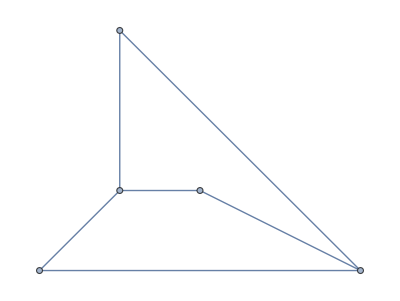
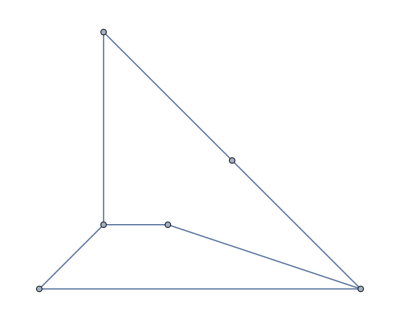
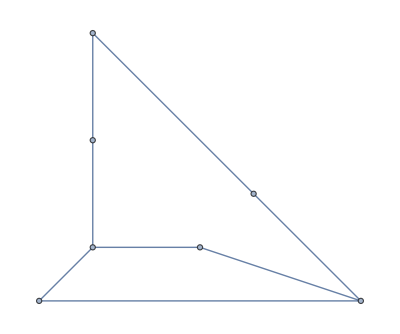
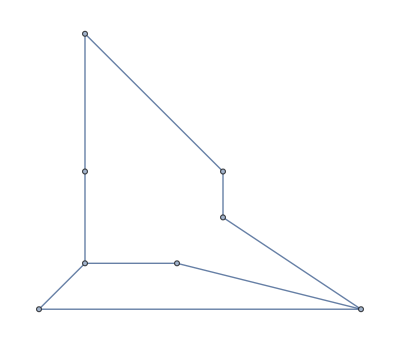
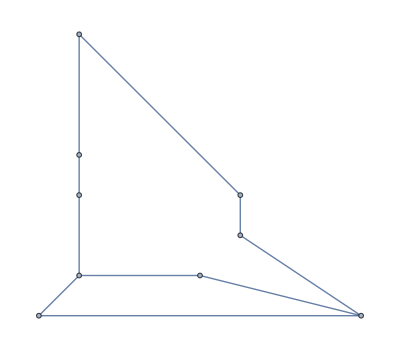
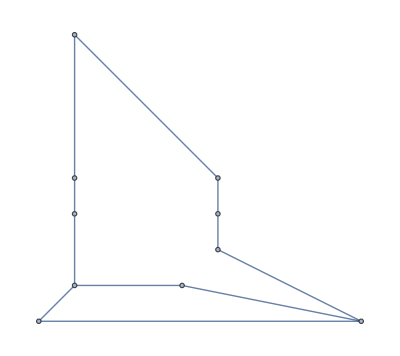
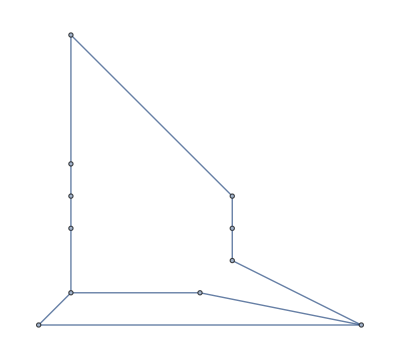
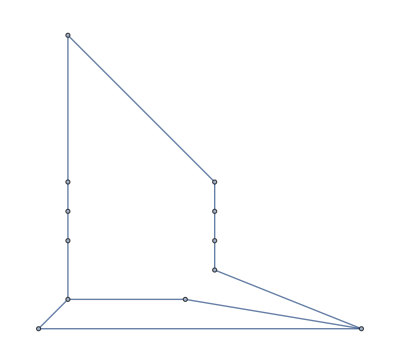
{{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-},{11,-Graphics-},{12,-Graphics-},{13,-Graphics-},{14,-Graphics-},{15,-Graphics-},{16,-Graphics-},{17,-Graphics-},{18,-Graphics-},{19,-Graphics-},{20,-Graphics-},{21,-Graphics-}}

```mathematica
Monitor[Table[With[{g=MinimalGraph[k]},{VertexCount[g],Graph[CollectMPGEdges[g],GraphLayout->"PlanarEmbedding"]}],{k,4,20}],k]
```

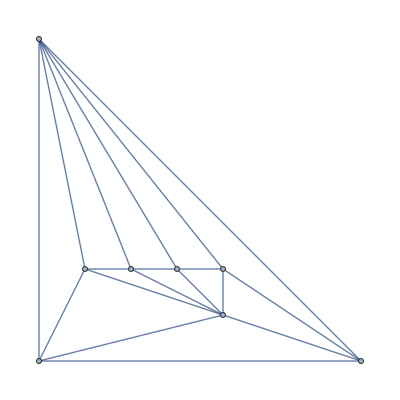
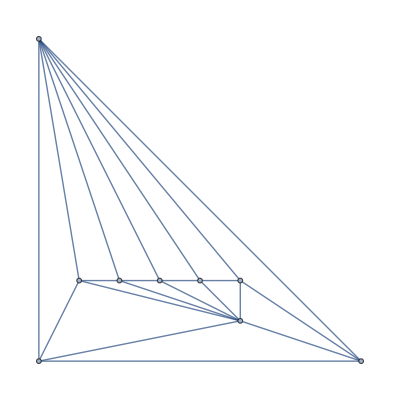
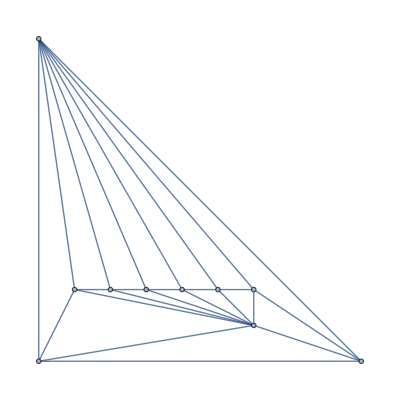
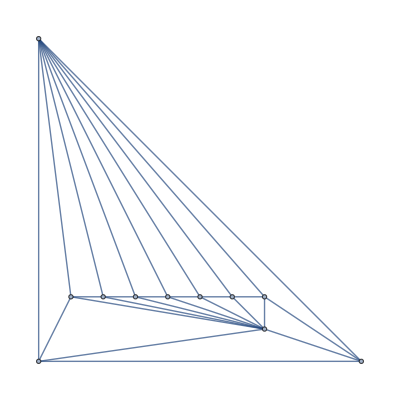
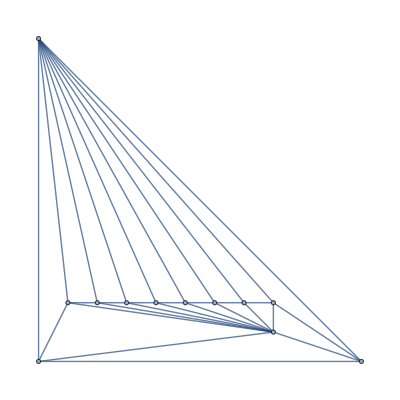
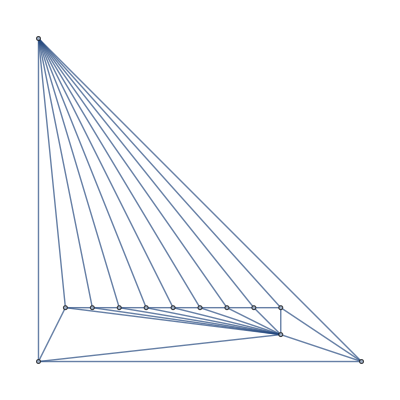
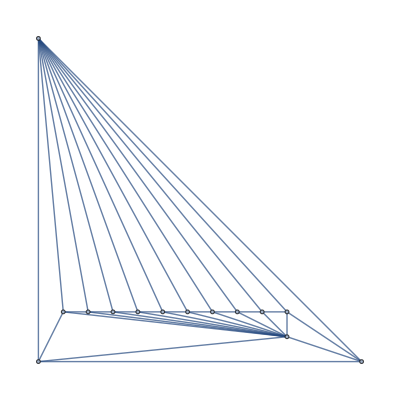
{{8,-Graphics-},{9,-Graphics-},{10,-Graphics-},{11,-Graphics-},{12,-Graphics-},{13,-Graphics-},{14,-Graphics-}}

```mathematica
Monitor[Table[With[{g=JacobsThalGraph[k]},{VertexCount[g],Graph[CollectMPGEdges[g],GraphLayout->"PlanarEmbedding"]}],{k,4,10}],k]
```